```mathematica
RandomReal[{1/5,2}]
```

0.635051

```mathematica
plotThemes={"Scientific","Monochrome","Detailed","Marketing","Classic"};
```

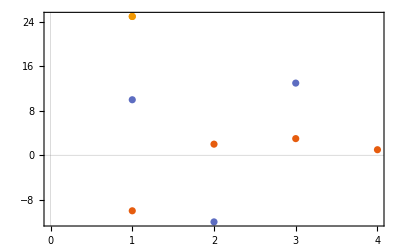
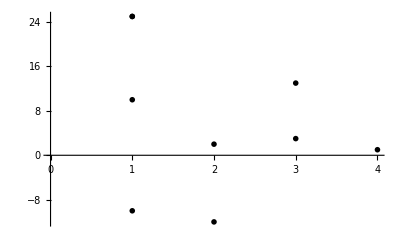
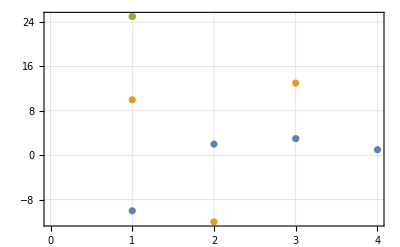
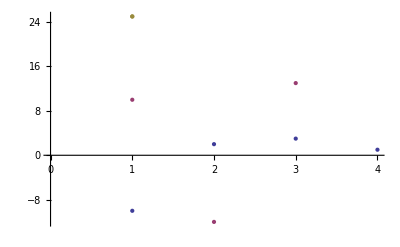
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[{{-10,2,3,1},{10,-12,13},{25}},PlotTheme->i],{i,plotThemes}]
```

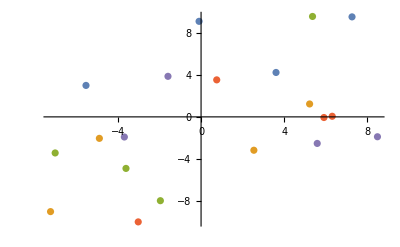

```mathematica
ListPlot@Partition[RandomReal[{-10,10},{21,2}],Round[21/5]]
```

```mathematica
RandomChoice[]
```

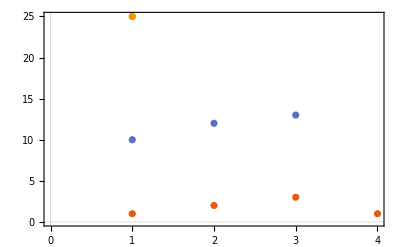

```mathematica
ListPlot[{{1,2,3,1},{10,12,13},{25}},PlotTheme->"Scientific"]
```

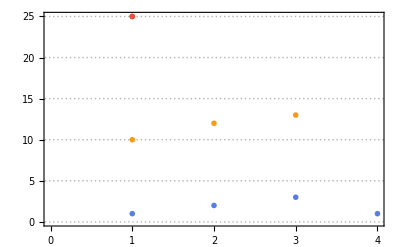

```mathematica
ListPlot[{{1,2,3,1},{10,12,13},{25}},PlotTheme->"Business"]
```

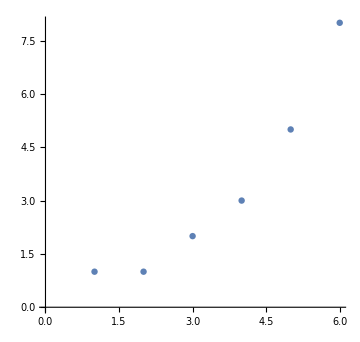

```mathematica
ListPlot[{1,1,2,3,5,8},ImageSize->{360,240},AspectRatio->RandomReal[{1/5,2}],Method->"GaussianMixture"]
```

```mathematica
ListPlot@Partition[RandomReal[{-10,10},{21,2}],Round[21/5]]
```

```mathematica
getRandomPointsList[range_,n_Integer,i_Integer] := Table[Partition[ RandomReal[ range, {n,2}], Round[n/5]],i ]
```

```mathematica
getRandomPointsList[{-100,100},20,1]
```

{{{{-95.3897,-71.876},{-88.2831,58.5994},{68.989,66.3747},{74.8136,7.85737}},{{-12.4425,-77.5274},{15.7339,-39.63},{44.3442,33.6676},{-50.8391,82.6184}},{{21.3255,44.5583},{-45.5031,21.9462},{-97.3034,43.1172},{6.71783,-5.35754}},{{15.4977,-40.4162},{79.0132,49.1641},{-40.9868,-97.7577},{86.5339,39.5146}},{{-0.00871358,-87.4318},{2.15913,37.2405},{-57.443,32.4398},{92.1403,98.4275}}}}

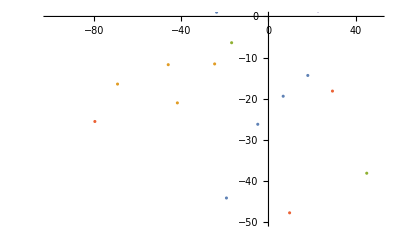

```mathematica
ListPlot[First@getRandomPointsList[{-500,500},1500,1],PlotRange->{{-100,50},{-50,0}}]
```

```mathematica
,
```

```mathematica
Part[createTrainingData[50,50,1],1,2]//Colorize
```

-Graphics-

```mathematica
RotationTransform[Part[createTrainingData[50,50,1],1,2],90]//Colorize
```

```mathematica
Rotate
```